{}

{{x→InterpolatingFunction[{{0., 1000.}}, <>],x2→InterpolatingFunction[{{0., 1000.}}, <>]}}

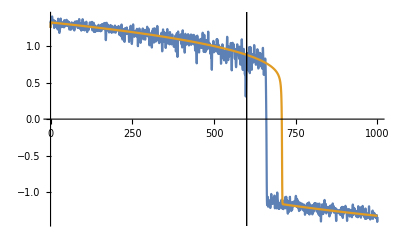

```mathematica
(* --------------   Tipping Model with white Noise ----------*)
Clear[x,F,t,tmax,zero,ans,data,Trend,NTrend,proc,n,F,t,s,noise,x2]
TMCWN=List[]
n=1000;
F=(2/n)*t -1;
noise=Interpolation[Table[{i,RandomReal[NormalDistribution[0,0.2]]},{i,0,n}]];
s=NDSolve[{x'[t]==-x[t]^3+x[t]-F+noise[t], x2'[t]==-x2[t]^3+x2[t]-F ,x[0]==1.25, x2[0]==1.25},{x,x2},{t,0,n}]
Plot[{Evaluate[x[t]/.s], Evaluate[x2[t]/.s]},{t,0,n},PlotRange->All,Epilog->{InfiniteLine[{600,0},{0,1}]}]
```

```mathematica
TMCWN=List[]
TMCWN=AppendTo[TMCWN,{1,2}];
TMCWN=AppendTo[TMCWN,{3,4}];
TMCWN=AppendTo[TMCWN,{5,6}];
TMCWN//MatrixForm
```

{}

(1 | 2
3 | 4
5 | 6)

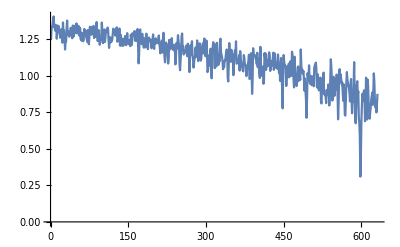

```mathematica
Clear[signal]
signal ={};
Do[
AppendTo[signal,Evaluate[x[i]/.s][[1]]]
,{i,0,630,1}]

ListLinePlot[signal]
```

```mathematica
Export["/Users/lha305/Desktop//TMCWN.csv",signal]
```

/Users/lha305/Desktop//TMCWN.csv

```mathematica
(* --------------   Tipping Model with time dependent Red Noise ----------*)
Clear[x,F,t,tmax,zero,ans,data,Trend,NTrend,proc,n,F,t,s,noise,x2]
Clear[n,noise,phi,sigma,no,phio,sigmao]
Clear[x,F,t,tmax,zero,ans,data,Trend,NTrend,proc,n,F,t,s,noise,x2,ARe,AR,noise2,noisew]
F=(2/n)*t -1;
n=1000;
noise ={};
phi={};
sigma={};
no=0;
phio = 0.1;
sigmao=0.13;
Do[
AppendTo[noise,no];
AppendTo[phi,phio];
AppendTo[sigma,sigmao];

phio = ((i*0.85)/n)+0.1;
(*sigmao= ((i*0.15)/n)+0.1 ;*)

no = phio*no + RandomReal[NormalDistribution[0,sigmao]],
{i,0,n}]
(*ListLinePlot[phi]
ListLinePlot[sigma]
ListLinePlot[noise]*)
cont=Interpolation[noise];
(*Plot[cont[t],{t,1,n+1}, PlotRange->All]*)

s=NDSolve[{x'[t]==-x[t]^3+x[t]-F+cont[t+1], x2'[t]==-x2[t]^3+x2[t]-F ,x[0]==1, x2[0]==1},{x,x2},{t,0,n}]
```

{{x→InterpolatingFunction[…],x2→InterpolatingFunction[…]}}

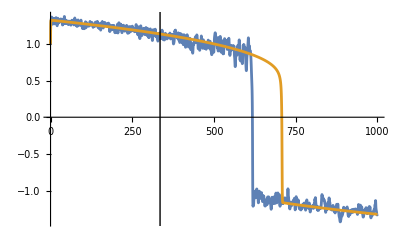

```mathematica
Plot[{Evaluate[x[t]/.s], Evaluate[x2[t]/.s]},{t,0,n},PlotRange->All,Epilog->{InfiniteLine[{335,0},{0,1}]}]
```

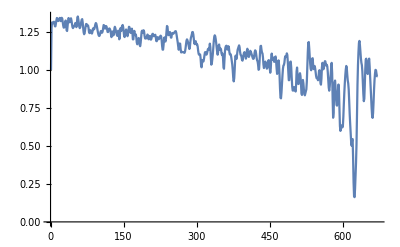

```mathematica
Clear[signal]
signal ={};
Do[
AppendTo[signal,Evaluate[x[i]/.s][[1]]]
,{i,0,335,0.5}]

ListLinePlot[signal]
```

```mathematica
Export["/Users/lha305/Desktop//TMTDRN.csv",signal]
```

/Users/lha305/Desktop//TMTDRN.csv

{{x→InterpolatingFunction[…],x2→InterpolatingFunction[…]}}

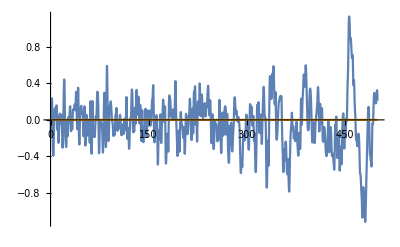

```mathematica
(* --------------   Non-Tipping Model with time dependent Red Noise ----------*)

Clear[n,noise,phi,sigma,no,phio,sigmao]
Clear[x,F,t,tmax,zero,ans,data,Trend,NTrend,proc,n,F,t,s,noise,x2,ARe,AR,noise2,noisew]
n=500;
noise ={};
phi={};
sigma={};
no=0;
phio = 0.1;
sigmao=1;
Do[
AppendTo[noise,no];
AppendTo[phi,phio];
AppendTo[sigma,sigmao];

phio = ((i*0.85)/n)+0.1;
(*sigmao= ((i*0.8)/n)+0.2 ;*)

no = phio*no + RandomReal[NormalDistribution[0,sigmao]],
{i,0,n}]
(*ListLinePlot[phi]
ListLinePlot[sigma]
ListLinePlot[noise]*)
cont=Interpolation[noise];
(*Plot[cont[t],{t,1,n+1}, PlotRange->All]*)

s=NDSolve[{x'[t]==-5*x[t]+ cont[t+1], x2'[t]==-5*x2[t] ,x[0]==0, x2[0]==0},{x,x2},{t,0,n}]
Plot[{Evaluate[x[t]/.s], Evaluate[x2[t]/.s]},{t,0,n},PlotRange->All]
```

```mathematica
signal ={};


Do[
AppendTo[signal,Evaluate[x[i]/.s][[1]]]
,{i,0,500,1}]
```

```mathematica
Export["/Users/lha305/Desktop//NTMTDRN.csv",signal]
```

/Users/lha305/Desktop//NTMTDRN.csv

TemporalData[…]

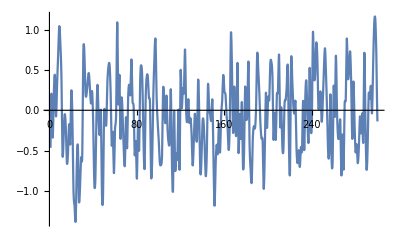

{{x→InterpolatingFunction[…],x2→InterpolatingFunction[…]}}

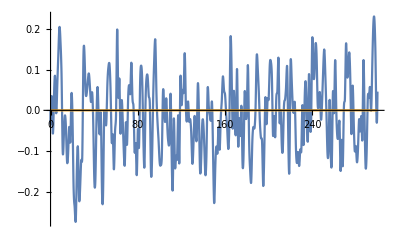

```mathematica
(* --------------   Non-Tipping Model Constant Red Noise ----------*)

Clear[n,noise,phi,sigma,no,phio,sigmao]
Clear[x,F,t,tmax,zero,ans,data,Trend,NTrend,proc,n,F,t,s,noise,x2,ARe,AR,noise2,noisew]
n=300;
noise = RandomFunction[ARProcess[{0.5},0.2],{0,n}]

cont=Interpolation[noise[[2]][[1]][[1]]];
Plot[cont[t],{t,1,n}, PlotRange->All]

s=NDSolve[{x'[t]==-5*x[t]+ cont[t+1], x2'[t]==-5*x2[t] ,x[0]==0, x2[0]==0},{x,x2},{t,0,n}]
Plot[{Evaluate[x[t]/.s], Evaluate[x2[t]/.s]},{t,0,n},PlotRange->All]
```

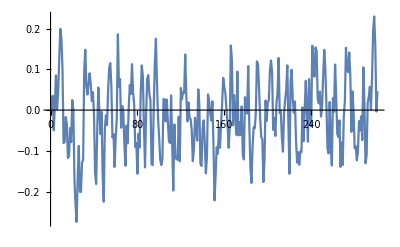

```mathematica
signal ={};


Do[
AppendTo[signal,Evaluate[x[i]/.s][[1]]]
,{i,0,n,1}]

ListLinePlot[signal]
```

```mathematica
Export["/Users/lha305/Desktop//NTMCRN.csv",signal]
```

/Users/lha305/Desktop//NTMCRN.csv

{{x→InterpolatingFunction[…],x2→InterpolatingFunction[…]}}

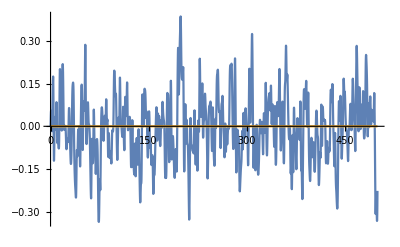

```mathematica
(* --------------   Non tipping Model Constant Red Noise ----------*)

Clear[n,noise,phi,sigma,no,phio,sigmao]
Clear[x,F,t,tmax,zero,ans,data,Trend,NTrend,proc,n,F,t,s,noise,x2,ARe,AR,noise2,noisew]
n=500;
noise ={};
phi={};
sigma={};
no=0;
phio = 0.1;
sigmao=0.2;
Do[
AppendTo[noise,no];
AppendTo[phi,phio];
AppendTo[sigma,sigmao];

phio = 0.5;
sigmao= 0.5 ;

no = phio*no + RandomReal[NormalDistribution[0,sigmao]],
{i,0,n}]
(*ListLinePlot[phi]
ListLinePlot[sigma]
ListLinePlot[noise]*)
cont=Interpolation[noise];
(*Plot[cont[t],{t,1,n+1}, PlotRange->All]*)

s=NDSolve[{x'[t]==-5*x[t]+ cont[t+1], x2'[t]==-5*x2[t] ,x[0]==0, x2[0]==0},{x,x2},{t,0,n}]
Plot[{Evaluate[x[t]/.s], Evaluate[x2[t]/.s]},{t,0,n},PlotRange->All]
```

```mathematica
signal ={};


Do[
AppendTo[signal,Evaluate[x[i]/.s][[1]]]
,{i,0,500,1}]
```

```mathematica
Export["/Users/lha305/Desktop//NTMCRN.csv",signal]
```

/Users/lha305/Desktop//NTMCRN.csv

```mathematica
(* --------------   Tipping Model with Constamt Red Noise ----------*)
Clear[x,F,t,tmax,zero,ans,data,Trend,NTrend,proc,n,F,t,s,noise,x2]
Clear[n,noise,phi,sigma,no,phio,sigmao]
Clear[x,F,t,tmax,zero,ans,data,Trend,NTrend,proc,n,F,t,s,noise,x2,ARe,AR,noise2,noisew]
F=(2/n)*t -1;
n=1000;
noise ={};
phi={};
sigma={};
no=0;
phio = 0.1;
sigmao=0.08;
Do[
AppendTo[noise,no];
AppendTo[phi,phio];
AppendTo[sigma,sigmao];

phio = 0.9;
(*sigmao= 0.15 ;*)

no = phio*no + RandomReal[NormalDistribution[0,sigmao]],
{i,0,n}]
(*ListLinePlot[phi]
ListLinePlot[sigma]
ListLinePlot[noise]*)
cont=Interpolation[noise];
(*Plot[cont[t],{t,1,n+1}, PlotRange->All]*)

s=NDSolve[{x'[t]==-x[t]^3+x[t]-F+cont[t+1], x2'[t]==-x2[t]^3+x2[t]-F ,x[0]==1, x2[0]==1},{x,x2},{t,0,n}]
```

{{x→InterpolatingFunction[…],x2→InterpolatingFunction[…]}}

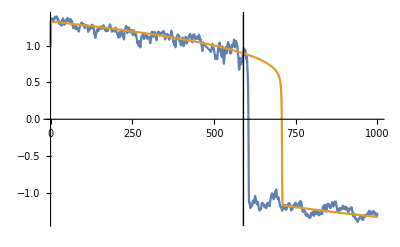

```mathematica
Plot[{Evaluate[x[t]/.s], Evaluate[x2[t]/.s]},{t,0,n},PlotRange->All,Epilog->{InfiniteLine[{590,0},{0,1}]}]
```

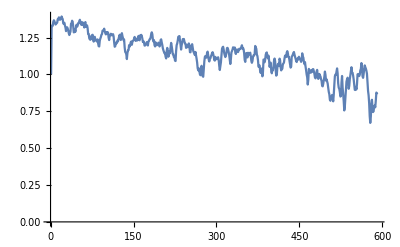

```mathematica
Clear[signal]
signal ={};
Do[
AppendTo[signal,Evaluate[x[i]/.s][[1]]]
,{i,0,590,1}]

ListLinePlot[signal]
```

```mathematica
Export["/Users/lha305/Desktop//TMCRN.csv",signal]
```

/Users/lha305/Desktop//TMCRN.csv